### Problem 1

```mathematica
A=({{0, 0, 2}, {0, 0, -2}, {2, -2, 2}});
```

```mathematica
(P=Transpose@(Normalize/@Eigenvectors[A]))//MatrixForm
```

(1/(√6) | -1/(√3) | 1/(√2)
-1/(√6) | 1/(√3) | 1/(√2)
√(2/3) | 1/(√3) | 0)

```mathematica
TeXForm@%
```

\left(
\begin{array}{ccc}
 \frac{1}{\sqrt{6}} & -\frac{1}{\sqrt{3}} & \frac{1}{\sqrt{2}}
   \\
 -\frac{1}{\sqrt{6}} & \frac{1}{\sqrt{3}} & \frac{1}{\sqrt{2}}
   \\
 \sqrt{\frac{2}{3}} & \frac{1}{\sqrt{3}} & 0 \\
\end{array}
\right)

```mathematica
Transpose@P-Inverse@P//Simplify//MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
d=Inverse[P].A.P//Simplify//MatrixForm
```

(4 | 0 | 0
0 | -2 | 0
0 | 0 | 0)

```mathematica
TeXForm@%
```

\left(
\begin{array}{ccc}
 4 & 0 & 0 \\
 0 & -2 & 0 \\
 0 & 0 & 0 \\
\end{array}
\right)

```mathematica
P[[2]].P[[3]]
```

0

```mathematica
{x,y}.({{-1, 2}, {2, 2}}).({{x}, {y}})//Simplify
```

{-x^2+4 x y+2 y^2}

```mathematica
A=({{-1, 2}, {2, 2}})
```

{{-1,2},{2,2}}

```mathematica
Eige
```

```mathematica
(P=Transpose@(Normalize/@Eigenvectors[A]))//MatrixForm
```

(1/(√5) | -2/(√5)
2/(√5) | 1/(√5))

```mathematica
TeXForm@%
```

\left(
\begin{array}{cc}
 \frac{1}{\sqrt{5}} & -\frac{2}{\sqrt{5}} \\
 \frac{2}{\sqrt{5}} & \frac{1}{\sqrt{5}} \\
\end{array}
\right)

```mathematica
Inverse[P].A.P//MatrixForm
```

(3 | 0
0 | -2)

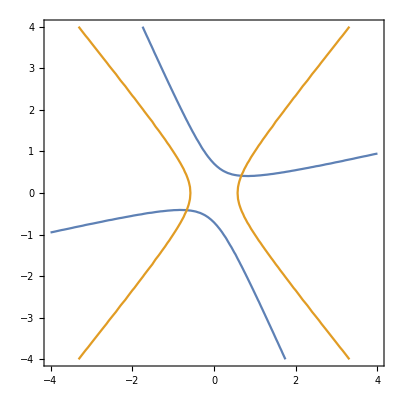

```mathematica
ContourPlot[{{-x^2+2y^2+4x y==1},{3x^2-2y^2==1}},{x,-4,4},{y,-4,4}]
```

```mathematica
u1={4,3I,-3-I}
```

{4,3 ⅈ,-3-ⅈ}

```mathematica
u2={I,1-I,-1}
```

{ⅈ,1-ⅈ,-1}

```mathematica
v={-4+5I,-5+3I,-7+4I}
```

{-4+5 ⅈ,-5+3 ⅈ,-7+4 ⅈ}

```mathematica
v={5-4I,3-5I,4-7I}
```

{5-4 ⅈ,3-5 ⅈ,4-7 ⅈ}

```mathematica
v={-4-5I,-5-3I,-7-4I}
```

{-4-5 ⅈ,-5-3 ⅈ,-7-4 ⅈ}

```mathematica
v={-4-4I,-4-4I,-8-4I}
```

{-4-4 ⅈ,-4-4 ⅈ,-8-4 ⅈ}

```mathematica
u1.v
```

0

```mathematica
{0,I,0}.{0,I,0}
```

-1

```mathematica
prod[a_,b_]:=Conjugate[a].b
```

```mathematica
prod[{0,I,0},{0,I,0}]
```

1

```mathematica
{prod[v,u1],prod[v,u2]}
```

{0,4}

```mathematica
u1={-2,I,I,1};
u2={I,1,2,5I};
```

```mathematica
v={-5,0,6I,-9}
```

{-5,0,6 ⅈ,-9}

```mathematica
prod[u1,u1]
```

7

```mathematica
prod[u2,u2]
```

31

```mathematica
prod[u1,v]
```

7

```mathematica
prod[v,u1]
```

7

```mathematica
prod[u2,v]
```

62 ⅈ

```mathematica
prod[v,u2]
```

-62 ⅈ

```mathematica
Minimize[prod[a u1 + b u2 -v,a u1 + b u2 -v],{a,b},Reals]
```

Minimize::objc: The objective function (5-2 a+ⅈ b) (5-2 Conjugate[a]-ⅈ Conjugate[b])+(9+a+5 ⅈ b) (9+Conjugate[a]-5 ⅈ Conjugate[b])+(ⅈ a+b) (-ⅈ Conjugate[a]+Conjugate[b])+(-6 ⅈ+ⅈ a+2 b) (6 ⅈ-ⅈ Conjugate[a]+2 Conjugate[b]) contains a nonreal constant ⅈ.

Minimize[(5-2 a+ⅈ b) (5-2 Conjugate[a]-ⅈ Conjugate[b])+(9+a+5 ⅈ b) (9+Conjugate[a]-5 ⅈ Conjugate[b])+(ⅈ a+b) (-ⅈ Conjugate[a]+Conjugate[b])+(-6 ⅈ+ⅈ a+2 b) (6 ⅈ-ⅈ Conjugate[a]+2 Conjugate[b]),{a,b},ℝ]

```mathematica
prod[a u1 + b u2 -v,a u1 + b u2 -v]//Simplify
```

142-7 a+62 ⅈ b+7 (-1+a) Conjugate[a]+31 (-2 ⅈ+b) Conjugate[b]

```mathematica
142-7 a+62 ⅈ b+7 (-1+a) a+31 (-2 ⅈ+b)b//Simplify
```

142-14 a+7 a^2+31 b^2

```mathematica
Minimize[142-14 a+7 a^2+31 b^2,{a,b}]
```

{135,{a→1,b→0}}

```mathematica
prod[u1,u2]
```

0

```mathematica
prod[v,u1]/prod[u1,u1]*u1+prod[v,u2]/prod[u2,u2]*u2
```

{0,-ⅈ,-3 ⅈ,11}

```mathematica
prod[v,u2]
```

-62 ⅈ